```mathematica
res = NDSolve[{u'[x] == Sin[1.4*(u[x])^2]-x+v[x], v'[x] == x+u[x]-(2.2*(v[x])^2)+1, u[0] == 1, v[0] == 0.5}, {u,v}, {x, 0, 5}];
```

```mathematica
UV = Part[res, 1];
U = Part[UV, 1];
V = Part[UV, 2];
```

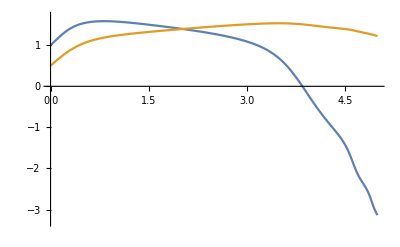

```mathematica
Plot[{u[x]/.U, v[x]/.V}, {x, 0, 5}, PlotRange->{-3.3, 1.7}]
```